```mathematica
r={0,y,z}-{R Cos[θ],R Sin[θ],0}
```

{-R Cos[θ],y-R Sin[θ],z}

```mathematica
dl={-Sin[θ],Cos[θ],0}R ⅆθ
```

{-R ⅆθ Sin[θ],R Cos[θ] ⅆθ,0}

```mathematica
Cross[dl,r]
```

{R z Cos[θ] ⅆθ,R z ⅆθ Sin[θ],R^2 Cos[θ]^2 ⅆθ-R y ⅆθ Sin[θ]+R^2 ⅆθ Sin[θ]^2}

```mathematica
FullSimplify@%
```

{R z Cos[θ] ⅆθ,R z ⅆθ Sin[θ],R ⅆθ (R-y Sin[θ])}

```mathematica
Norm[r]
```

√(Abs[z]^2+Abs[R Cos[θ]]^2+Abs[y-R Sin[θ]]^2)

```mathematica
%6/.Abs->Identity
```

√(z^2+R^2 Cos[θ]^2+(y-R Sin[θ])^2)

```mathematica
Simplify@%
```

√(R^2+y^2+z^2-2 R y Sin[θ])

```mathematica
(%4)/(%10^3)
```

{(R z Cos[θ] ⅆθ)/((R^2+y^2+z^2-2 R y Sin[θ])^(3/2)),(R z ⅆθ Sin[θ])/((R^2+y^2+z^2-2 R y Sin[θ])^(3/2)),(R ⅆθ (R-y Sin[θ]))/((R^2+y^2+z^2-2 R y Sin[θ])^(3/2))}

```mathematica
%11/.ⅆθ->1
```

{(R z Cos[θ])/((R^2+y^2+z^2-2 R y Sin[θ])^(3/2)),(R z Sin[θ])/((R^2+y^2+z^2-2 R y Sin[θ])^(3/2)),(R (R-y Sin[θ]))/((R^2+y^2+z^2-2 R y Sin[θ])^(3/2))}

```mathematica
R=1;
```

```mathematica
dBfy[y_,z_,θ_]:=(R z Sin[θ])/((R^2+y^2+z^2-2 R y Sin[θ])^(3/2));
dBfz[y_,z_,θ_]:=(R (R-y Sin[θ]))/((R^2+y^2+z^2-2 R y Sin[θ])^(3/2));
By[y_,z_]:=2NIntegrate[dBfy[y,z,θ],{θ,-0.5π,0.5π}];
Bz[y_,z_]:=2NIntegrate[dBfz[y,z,θ],{θ,-0.5π,0.5π}];
```

```mathematica
points=Tuples[Range[-2,2,0.2],2];
```

```mathematica
field=Through[{By,Bz}[##]]&@@@points;
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate :: izero will be suppressed during this calculation.

NIntegrate::zeroregion: Integration region {{-1.5708, -1.5707963267948897987109854090766909024065913640317254760126602919}} cannot be further subdivided at the specified working precision. NIntegrate assumes zero integral there and on any further indivisible regions.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {-1.5707962704498600439294607254167937277627986603079079941380769014}. NIntegrate obtained 9.75225 and 0.26418 for the integral and error estimates.

NIntegrate::zeroregion: Integration region {{1.5708, 1.5707963267948897987109854090766909024065913640317254760126602919}} cannot be further subdivided at the specified working precision. NIntegrate assumes zero integral there and on any further indivisible regions.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.5707962704498600439294607254167937277627986603079079941380769014}. NIntegrate obtained 9.75225 and 0.26418 for the integral and error estimates.

```mathematica
Thread[{points,field}];
```

{{{-2.,-2.},{0.197197,0.0890344}},{{-2.,-1.8},{0.233278,0.0829009}},{{-2.,-1.6},{0.274368,0.0689339}},{{-2.,-1.4},{0.319279,0.0433319}},{{-2.,-1.2},{0.364807,0.00117455}},{{-2.,-1.},{0.404223,-0.0631029}},{{-2.,-0.8},{0.425372,-0.153853}},{{-2.,-0.6},{0.409678,-0.269712}},{{-2.,-0.4},{0.335786,-0.396169}},{{-2.,-0.2},{0.192913,-0.500433}},{{-2.,0.},{0.,-0.541732}},{{-2.,0.2},{-0.192913,-0.500433}},{{-2.,0.4},{-0.335786,-0.396169}},{{-2.,0.6},{-0.409678,-0.269712}},{{-2.,0.8},{-0.425372,-0.153853}},{{-2.,1.},{-0.404223,-0.0631029}},{{-2.,1.2},{-0.364807,0.00117455}},{{-2.,1.4},{-0.319279,0.0433319}},{{-2.,1.6},{-0.274368,0.0689339}},{{-2.,1.8},{-0.233278,0.0829009}},{{-2.,2.},{-0.197197,0.0890344}},{{-1.8,-2.},{0.219297,0.126826}},{{-1.8,-1.8},{0.265896,0.12769}},{{-1.8,-1.6},{0.321976,0.120828}},{{-1.8,-1.4},{0.387956,0.101063}},{{-1.8,-1.2},{0.46231,0.0605913}},{{-1.8,-1.},{0.539055,-0.0116409}},{{-1.8,-0.8},{0.603076,-0.129169}},{{-1.8,-0.6},{0.623299,-0.302257}},{{-1.8,-0.4},{0.549684,-0.520595}},{{-1.8,-0.2},{0.335176,-0.725479}},{{-1.8,0.},{0.,-0.813398}},{{-1.8,0.2},{-0.335176,-0.725479}},{{-1.8,0.4},{-0.549684,-0.520595}},{{-1.8,0.6},{-0.623299,-0.302257}},{{-1.8,0.8},{-0.603076,-0.129169}},{{-1.8,1.},{-0.539055,-0.0116409}},{{-1.8,1.2},{-0.46231,0.0605913}},{{-1.8,1.4},{-0.387956,0.101063}},{{-1.8,1.6},{-0.321976,0.120828}},{{-1.8,1.8},{-0.265896,0.12769}},{{-1.8,2.},{-0.219297,0.126826}},{{-1.6,-2.},{0.23802,0.173522}},{{-1.6,-1.8},{0.295691,0.185628}},{{-1.6,-1.6},{0.368631,0.192054}},{{-1.6,-1.4},{0.46025,0.186946}},{{-1.6,-1.2},{0.573371,0.160119}},{{-1.6,-1.},{0.707616,0.0941377}},{{-1.6,-0.8},{0.852303,-0.0395719}},{{-1.6,-0.6},{0.968877,-0.281583}},{{-1.6,-0.4},{0.957823,-0.66238}},{{-1.6,-0.2},{0.650937,-1.1085}},{{-1.6,0.},{0.,-1.33154}},{{-1.6,0.2},{-0.650937,-1.1085}},{{-1.6,0.4},{-0.957823,-0.66238}},{{-1.6,0.6},{-0.968877,-0.281583}},{{-1.6,0.8},{-0.852303,-0.0395719}},{{-1.6,1.},{-0.707616,0.0941377}},{{-1.6,1.2},{-0.573371,0.160119}},{{-1.6,1.4},{-0.46025,0.186946}},{{-1.6,1.6},{-0.368631,0.192054}},{{-1.6,1.8},{-0.295691,0.185628}},{{-1.6,2.},{-0.23802,0.173522}},{{-1.4,-2.},{0.250345,0.228724}},{{-1.4,-1.8},{0.318169,0.256949}},{{-1.4,-1.6},{0.407679,0.284389}},{{-1.4,-1.4},{0.526509,0.306265}},{{-1.4,-1.2},{0.68482,0.312774}},{{-1.4,-1.},{0.895152,0.283809}},{{-1.4,-0.8},{1.16877,0.177373}},{{-1.4,-0.6},{1.49622,-0.0950292}},{{-1.4,-0.4},{1.76303,-0.702395}},{{-1.4,-0.2},{1.49284,-1.7736}},{{-1.4,0.},{0.,-2.52635}},{{-1.4,0.2},{-1.49284,-1.7736}},{{-1.4,0.4},{-1.76303,-0.702395}},{{-1.4,0.6},{-1.49622,-0.0950292}},{{-1.4,0.8},{-1.16877,0.177373}},{{-1.4,1.},{-0.895152,0.283809}},{{-1.4,1.2},{-0.68482,0.312774}},{{-1.4,1.4},{-0.526509,0.306265}},{{-1.4,1.6},{-0.407679,0.284389}},{{-1.4,1.8},{-0.318169,0.256949}},{{-1.4,2.},{-0.250345,0.228724}},{{-1.2,-2.},{0.253005,0.290654}},{{-1.2,-1.8},{0.328086,0.339711}},{{-1.2,-1.6},{0.430567,0.396156}},{{-1.2,-1.4},{0.572505,0.458904}},{{-1.2,-1.2},{0.772567,0.523722}},{{-1.2,-1.},{1.06088,0.578648}},{{-1.2,-0.8},{1.48866,0.591191}},{{-1.2,-0.6},{2.14643,0.466302}},{{-1.2,-0.4},{3.17236,-0.1211}},{{-1.2,-0.2},{4.27018,-2.43864}},{{-1.2,0.},{0.,-6.69063}},{{-1.2,0.2},{-4.27018,-2.43864}},{{-1.2,0.4},{-3.17236,-0.1211}},{{-1.2,0.6},{-2.14643,0.466302}},{{-1.2,0.8},{-1.48866,0.591191}},{{-1.2,1.},{-1.06088,0.578648}},{{-1.2,1.2},{-0.772567,0.523722}},{{-1.2,1.4},{-0.572505,0.458904}},{{-1.2,1.6},{-0.430567,0.396156}},{{-1.2,1.8},{-0.328086,0.339711}},{{-1.2,2.},{-0.253005,0.290654}},{{-1.,-2.},{0.243091,0.355979}},{{-1.,-1.8},{0.320495,0.429304}},{{-1.,-1.6},{0.428674,0.520947}},{{-1.,-1.4},{0.582642,0.635958}},{{-1.,-1.2},{0.806795,0.780934}},{{-1.,-1.},{1.14331,0.964832}},{{-1.,-0.8},{1.67257,1.20088}},{{-1.,-0.6},{2.5735,1.51184}},{{-1.,-0.4},{4.3637,1.94762}},{{-1.,-0.2},{9.5739,2.67137}},{{-1.,0.},{0.,19.5045}},{{-1.,0.2},{-9.5739,2.67137}},{{-1.,0.4},{-4.3637,1.94762}},{{-1.,0.6},{-2.5735,1.51184}},{{-1.,0.8},{-1.67257,1.20088}},{{-1.,1.},{-1.14331,0.964832}},{{-1.,1.2},{-0.806795,0.780934}},{{-1.,1.4},{-0.582642,0.635958}},{{-1.,1.6},{-0.428674,0.520947}},{{-1.,1.8},{-0.320495,0.429304}},{{-1.,2.},{-0.243091,0.355979}},{{-0.8,-2.},{0.218774,0.420026}},{{-0.8,-1.8},{0.292085,0.518722}},{{-0.8,-1.6},{0.395966,0.647883}},{{-0.8,-1.4},{0.545642,0.819633}},{{-0.8,-1.2},{0.765313,1.05302}},{{-0.8,-1.},{1.09463,1.3808}},{{-0.8,-0.8},{1.60115,1.86741}},{{-0.8,-0.6},{2.40339,2.66541}},{{-0.8,-0.4},{3.68226,4.2292}},{{-0.8,-0.2},{5.09385,8.16279}},{{-0.8,0.},{0.,14.1817}},{{-0.8,0.2},{-5.09385,8.16279}},{{-0.8,0.4},{-3.68226,4.2292}},{{-0.8,0.6},{-2.40339,2.66541}},{{-0.8,0.8},{-1.60115,1.86741}},{{-0.8,1.},{-1.09463,1.3808}},{{-0.8,1.2},{-0.765313,1.05302}},{{-0.8,1.4},{-0.545642,0.819633}},{{-0.8,1.6},{-0.395966,0.647883}},{{-0.8,1.8},{-0.292085,0.518722}},{{-0.8,2.},{-0.218774,0.420026}},{{-0.6,-2.},{0.179865,0.477397}},{{-0.6,-1.8},{0.242238,0.599663}},{{-0.6,-1.6},{0.331127,0.763748}},{{-0.6,-1.4},{0.459264,0.987843}},{{-0.6,-1.2},{0.645363,1.30035}},{{-0.6,-1.},{0.915336,1.74781}},{{-0.6,-0.8},{1.2986,2.41106}},{{-0.6,-0.6},{1.80038,3.43704}},{{-0.6,-0.4},{2.2741,5.06928}},{{-0.6,-0.2},{2.02367,7.38992}},{{-0.6,0.},{0.,8.86302}},{{-0.6,0.2},{-2.02367,7.38992}},{{-0.6,0.4},{-2.2741,5.06928}},{{-0.6,0.6},{-1.80038,3.43704}},{{-0.6,0.8},{-1.2986,2.41106}},{{-0.6,1.},{-0.915336,1.74781}},{{-0.6,1.2},{-0.645363,1.30035}},{{-0.6,1.4},{-0.459264,0.987843}},{{-0.6,1.6},{-0.331127,0.763748}},{{-0.6,1.8},{-0.242238,0.599663}},{{-0.6,2.},{-0.179865,0.477397}},{{-0.4,-2.},{0.128024,0.522818}},{{-0.4,-1.8},{0.173353,0.664056}},{{-0.4,-1.6},{0.237996,0.856002}},{{-0.4,-1.4},{0.33063,1.12079}},{{-0.4,-1.2},{0.462648,1.49121}},{{-0.4,-1.},{0.645833,2.01524}},{{-0.4,-0.8},{0.88189,2.75922}},{{-0.4,-0.6},{1.13025,3.79772}},{{-0.4,-0.4},{1.23844,5.14394}},{{-0.4,-0.2},{0.903869,6.52544}},{{-0.4,0.},{0.,7.17115}},{{-0.4,0.2},{-0.903869,6.52544}},{{-0.4,0.4},{-1.23844,5.14394}},{{-0.4,0.6},{-1.13025,3.79772}},{{-0.4,0.8},{-0.88189,2.75922}},{{-0.4,1.},{-0.645833,2.01524}},{{-0.4,1.2},{-0.462648,1.49121}},{{-0.4,1.4},{-0.33063,1.12079}},{{-0.4,1.6},{-0.237996,0.856002}},{{-0.4,1.8},{-0.173353,0.664056}},{{-0.4,2.},{-0.128024,0.522818}},{{-0.2,-2.},{0.0665665,0.551951}},{{-0.2,-1.8},{0.0903922,0.705418}},{{-0.2,-1.6},{0.124327,0.915106}},{{-0.2,-1.4},{0.172641,1.20505}},{{-0.2,-1.2},{0.240364,1.60901}},{{-0.2,-1.},{0.331007,2.17101}},{{-0.2,-0.8},{0.439353,2.93805}},{{-0.2,-0.6},{0.535216,3.93031}},{{-0.2,-0.4},{0.543568,5.0671}},{{-0.2,-0.2},{0.365338,6.06529}},{{-0.2,0.},{0.,6.47904}},{{-0.2,0.2},{-0.365338,6.06529}},{{-0.2,0.4},{-0.543568,5.0671}},{{-0.2,0.6},{-0.535216,3.93031}},{{-0.2,0.8},{-0.439353,2.93805}},{{-0.2,1.},{-0.331007,2.17101}},{{-0.2,1.2},{-0.240364,1.60901}},{{-0.2,1.4},{-0.172641,1.20505}},{{-0.2,1.6},{-0.124327,0.915106}},{{-0.2,1.8},{-0.0903922,0.705418}},{{-0.2,2.},{-0.0665665,0.551951}},{{0.,-2.},{0.,0.561985}},{{0.,-1.8},{0.,0.719666}},{{0.,-1.6},{0.,0.935416}},{{0.,-1.4},{0.,1.23379}},{{0.,-1.2},{0.,1.64852}},{{0.,-1.},{0.,2.22144}},{{0.,-0.8},{0.,2.99167}},{{0.,-0.6},{0.,3.96161}},{{0.,-0.4},{0.,5.02913}},{{0.,-0.2},{0.,5.9242}},{{0.,0.},{0.,6.28319}},{{0.,0.2},{0.,5.9242}},{{0.,0.4},{0.,5.02913}},{{0.,0.6},{0.,3.96161}},{{0.,0.8},{0.,2.99167}},{{0.,1.},{0.,2.22144}},{{0.,1.2},{0.,1.64852}},{{0.,1.4},{0.,1.23379}},{{0.,1.6},{0.,0.935416}},{{0.,1.8},{0.,0.719666}},{{0.,2.},{0.,0.561985}},{{0.2,-2.},{-0.0665665,0.551951}},{{0.2,-1.8},{-0.0903922,0.705418}},{{0.2,-1.6},{-0.124327,0.915106}},{{0.2,-1.4},{-0.172641,1.20505}},{{0.2,-1.2},{-0.240364,1.60901}},{{0.2,-1.},{-0.331007,2.17101}},{{0.2,-0.8},{-0.439353,2.93805}},{{0.2,-0.6},{-0.535216,3.93031}},{{0.2,-0.4},{-0.543568,5.0671}},{{0.2,-0.2},{-0.365338,6.06529}},{{0.2,0.},{0.,6.47904}},{{0.2,0.2},{0.365338,6.06529}},{{0.2,0.4},{0.543568,5.0671}},{{0.2,0.6},{0.535216,3.93031}},{{0.2,0.8},{0.439353,2.93805}},{{0.2,1.},{0.331007,2.17101}},{{0.2,1.2},{0.240364,1.60901}},{{0.2,1.4},{0.172641,1.20505}},{{0.2,1.6},{0.124327,0.915106}},{{0.2,1.8},{0.0903922,0.705418}},{{0.2,2.},{0.0665665,0.551951}},{{0.4,-2.},{-0.128024,0.522818}},{{0.4,-1.8},{-0.173353,0.664056}},{{0.4,-1.6},{-0.237996,0.856002}},{{0.4,-1.4},{-0.33063,1.12079}},{{0.4,-1.2},{-0.462648,1.49121}},{{0.4,-1.},{-0.645833,2.01524}},{{0.4,-0.8},{-0.88189,2.75922}},{{0.4,-0.6},{-1.13025,3.79772}},{{0.4,-0.4},{-1.23844,5.14394}},{{0.4,-0.2},{-0.903869,6.52544}},{{0.4,0.},{0.,7.17115}},{{0.4,0.2},{0.903869,6.52544}},{{0.4,0.4},{1.23844,5.14394}},{{0.4,0.6},{1.13025,3.79772}},{{0.4,0.8},{0.88189,2.75922}},{{0.4,1.},{0.645833,2.01524}},{{0.4,1.2},{0.462648,1.49121}},{{0.4,1.4},{0.33063,1.12079}},{{0.4,1.6},{0.237996,0.856002}},{{0.4,1.8},{0.173353,0.664056}},{{0.4,2.},{0.128024,0.522818}},{{0.6,-2.},{-0.179865,0.477397}},{{0.6,-1.8},{-0.242238,0.599663}},{{0.6,-1.6},{-0.331127,0.763748}},{{0.6,-1.4},{-0.459264,0.987843}},{{0.6,-1.2},{-0.645363,1.30035}},{{0.6,-1.},{-0.915336,1.74781}},{{0.6,-0.8},{-1.2986,2.41106}},{{0.6,-0.6},{-1.80038,3.43704}},{{0.6,-0.4},{-2.2741,5.06928}},{{0.6,-0.2},{-2.02367,7.38992}},{{0.6,0.},{0.,8.86302}},{{0.6,0.2},{2.02367,7.38992}},{{0.6,0.4},{2.2741,5.06928}},{{0.6,0.6},{1.80038,3.43704}},{{0.6,0.8},{1.2986,2.41106}},{{0.6,1.},{0.915336,1.74781}},{{0.6,1.2},{0.645363,1.30035}},{{0.6,1.4},{0.459264,0.987843}},{{0.6,1.6},{0.331127,0.763748}},{{0.6,1.8},{0.242238,0.599663}},{{0.6,2.},{0.179865,0.477397}},{{0.8,-2.},{-0.218774,0.420026}},{{0.8,-1.8},{-0.292085,0.518722}},{{0.8,-1.6},{-0.395966,0.647883}},{{0.8,-1.4},{-0.545642,0.819633}},{{0.8,-1.2},{-0.765313,1.05302}},{{0.8,-1.},{-1.09463,1.3808}},{{0.8,-0.8},{-1.60115,1.86741}},{{0.8,-0.6},{-2.40339,2.66541}},{{0.8,-0.4},{-3.68226,4.2292}},{{0.8,-0.2},{-5.09385,8.16279}},{{0.8,0.},{0.,14.1817}},{{0.8,0.2},{5.09385,8.16279}},{{0.8,0.4},{3.68226,4.2292}},{{0.8,0.6},{2.40339,2.66541}},{{0.8,0.8},{1.60115,1.86741}},{{0.8,1.},{1.09463,1.3808}},{{0.8,1.2},{0.765313,1.05302}},{{0.8,1.4},{0.545642,0.819633}},{{0.8,1.6},{0.395966,0.647883}},{{0.8,1.8},{0.292085,0.518722}},{{0.8,2.},{0.218774,0.420026}},{{1.,-2.},{-0.243091,0.355979}},{{1.,-1.8},{-0.320495,0.429304}},{{1.,-1.6},{-0.428674,0.520947}},{{1.,-1.4},{-0.582642,0.635958}},{{1.,-1.2},{-0.806795,0.780934}},{{1.,-1.},{-1.14331,0.964832}},{{1.,-0.8},{-1.67257,1.20088}},{{1.,-0.6},{-2.5735,1.51184}},{{1.,-0.4},{-4.3637,1.94762}},{{1.,-0.2},{-9.5739,2.67137}},{{1.,0.},{0.,19.5045}},{{1.,0.2},{9.5739,2.67137}},{{1.,0.4},{4.3637,1.94762}},{{1.,0.6},{2.5735,1.51184}},{{1.,0.8},{1.67257,1.20088}},{{1.,1.},{1.14331,0.964832}},{{1.,1.2},{0.806795,0.780934}},{{1.,1.4},{0.582642,0.635958}},{{1.,1.6},{0.428674,0.520947}},{{1.,1.8},{0.320495,0.429304}},{{1.,2.},{0.243091,0.355979}},{{1.2,-2.},{-0.253005,0.290654}},{{1.2,-1.8},{-0.328086,0.339711}},{{1.2,-1.6},{-0.430567,0.396156}},{{1.2,-1.4},{-0.572505,0.458904}},{{1.2,-1.2},{-0.772567,0.523722}},{{1.2,-1.},{-1.06088,0.578648}},{{1.2,-0.8},{-1.48866,0.591191}},{{1.2,-0.6},{-2.14643,0.466302}},{{1.2,-0.4},{-3.17236,-0.1211}},{{1.2,-0.2},{-4.27018,-2.43864}},{{1.2,0.},{0.,-6.69063}},{{1.2,0.2},{4.27018,-2.43864}},{{1.2,0.4},{3.17236,-0.1211}},{{1.2,0.6},{2.14643,0.466302}},{{1.2,0.8},{1.48866,0.591191}},{{1.2,1.},{1.06088,0.578648}},{{1.2,1.2},{0.772567,0.523722}},{{1.2,1.4},{0.572505,0.458904}},{{1.2,1.6},{0.430567,0.396156}},{{1.2,1.8},{0.328086,0.339711}},{{1.2,2.},{0.253005,0.290654}},{{1.4,-2.},{-0.250345,0.228724}},{{1.4,-1.8},{-0.318169,0.256949}},{{1.4,-1.6},{-0.407679,0.284389}},{{1.4,-1.4},{-0.526509,0.306265}},{{1.4,-1.2},{-0.68482,0.312774}},{{1.4,-1.},{-0.895152,0.283809}},{{1.4,-0.8},{-1.16877,0.177373}},{{1.4,-0.6},{-1.49622,-0.0950292}},{{1.4,-0.4},{-1.76303,-0.702395}},{{1.4,-0.2},{-1.49284,-1.7736}},{{1.4,0.},{0.,-2.52635}},{{1.4,0.2},{1.49284,-1.7736}},{{1.4,0.4},{1.76303,-0.702395}},{{1.4,0.6},{1.49622,-0.0950292}},{{1.4,0.8},{1.16877,0.177373}},{{1.4,1.},{0.895152,0.283809}},{{1.4,1.2},{0.68482,0.312774}},{{1.4,1.4},{0.526509,0.306265}},{{1.4,1.6},{0.407679,0.284389}},{{1.4,1.8},{0.318169,0.256949}},{{1.4,2.},{0.250345,0.228724}},{{1.6,-2.},{-0.23802,0.173522}},{{1.6,-1.8},{-0.295691,0.185628}},{{1.6,-1.6},{-0.368631,0.192054}},{{1.6,-1.4},{-0.46025,0.186946}},{{1.6,-1.2},{-0.573371,0.160119}},{{1.6,-1.},{-0.707616,0.0941377}},{{1.6,-0.8},{-0.852303,-0.0395719}},{{1.6,-0.6},{-0.968877,-0.281583}},{{1.6,-0.4},{-0.957823,-0.66238}},{{1.6,-0.2},{-0.650937,-1.1085}},{{1.6,0.},{0.,-1.33154}},{{1.6,0.2},{0.650937,-1.1085}},{{1.6,0.4},{0.957823,-0.66238}},{{1.6,0.6},{0.968877,-0.281583}},{{1.6,0.8},{0.852303,-0.0395719}},{{1.6,1.},{0.707616,0.0941377}},{{1.6,1.2},{0.573371,0.160119}},{{1.6,1.4},{0.46025,0.186946}},{{1.6,1.6},{0.368631,0.192054}},{{1.6,1.8},{0.295691,0.185628}},{{1.6,2.},{0.23802,0.173522}},{{1.8,-2.},{-0.219297,0.126826}},{{1.8,-1.8},{-0.265896,0.12769}},{{1.8,-1.6},{-0.321976,0.120828}},{{1.8,-1.4},{-0.387956,0.101063}},{{1.8,-1.2},{-0.46231,0.0605913}},{{1.8,-1.},{-0.539055,-0.0116409}},{{1.8,-0.8},{-0.603076,-0.129169}},{{1.8,-0.6},{-0.623299,-0.302257}},{{1.8,-0.4},{-0.549684,-0.520595}},{{1.8,-0.2},{-0.335176,-0.725479}},{{1.8,0.},{0.,-0.813398}},{{1.8,0.2},{0.335176,-0.725479}},{{1.8,0.4},{0.549684,-0.520595}},{{1.8,0.6},{0.623299,-0.302257}},{{1.8,0.8},{0.603076,-0.129169}},{{1.8,1.},{0.539055,-0.0116409}},{{1.8,1.2},{0.46231,0.0605913}},{{1.8,1.4},{0.387956,0.101063}},{{1.8,1.6},{0.321976,0.120828}},{{1.8,1.8},{0.265896,0.12769}},{{1.8,2.},{0.219297,0.126826}},{{2.,-2.},{-0.197197,0.0890344}},{{2.,-1.8},{-0.233278,0.0829009}},{{2.,-1.6},{-0.274368,0.0689339}},{{2.,-1.4},{-0.319279,0.0433319}},{{2.,-1.2},{-0.364807,0.00117455}},{{2.,-1.},{-0.404223,-0.0631029}},{{2.,-0.8},{-0.425372,-0.153853}},{{2.,-0.6},{-0.409678,-0.269712}},{{2.,-0.4},{-0.335786,-0.396169}},{{2.,-0.2},{-0.192913,-0.500433}},{{2.,0.},{0.,-0.541732}},{{2.,0.2},{0.192913,-0.500433}},{{2.,0.4},{0.335786,-0.396169}},{{2.,0.6},{0.409678,-0.269712}},{{2.,0.8},{0.425372,-0.153853}},{{2.,1.},{0.404223,-0.0631029}},{{2.,1.2},{0.364807,0.00117455}},{{2.,1.4},{0.319279,0.0433319}},{{2.,1.6},{0.274368,0.0689339}},{{2.,1.8},{0.233278,0.0829009}},{{2.,2.},{0.197197,0.0890344}}}

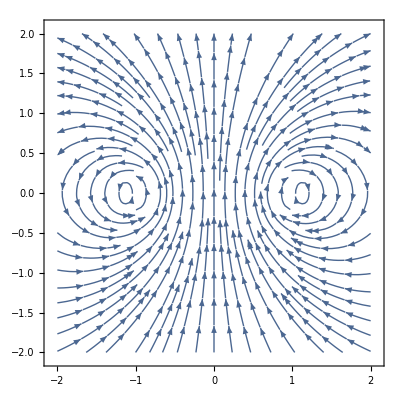

```mathematica
ListStreamPlot[%]
```

```mathematica
points0=Tuples[{Range[-2,2,0.2],Range[-4,4,0.2]}];
points1=Tuples[{Range[-2,2,0.2],Range[-5,3,0.2]}];
points2=Tuples[{Range[-2,2,0.2],Range[-3,5,0.2]}];
{field0,field1,field2}=(Through[{By,Bz}[##]]&@@@#)&/@{points0,points1,points2};
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate :: izero will be suppressed during this calculation.

NIntegrate::zeroregion: Integration region {{-1.5708, -1.5707963267948897987109854090766909024065913640317254760126602919}} cannot be further subdivided at the specified working precision. NIntegrate assumes zero integral there and on any further indivisible regions.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {-1.5707962704498600439294607254167937277627986603079079941380769014}. NIntegrate obtained 9.75225 and 0.26418 for the integral and error estimates.

NIntegrate::zeroregion: Integration region {{1.5708, 1.5707963267948897987109854090766909024065913640317254760126602919}} cannot be further subdivided at the specified working precision. NIntegrate assumes zero integral there and on any further indivisible regions.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.5707962704498600439294607254167937277627986603079079941380769014}. NIntegrate obtained 9.75225 and 0.26418 for the integral and error estimates.

NIntegrate::zeroregion: Integration region {{-1.5708, -1.5707963267948897987109854090766909024065913640317254760126602919}} cannot be further subdivided at the specified working precision. NIntegrate assumes zero integral there and on any further indivisible regions.

General::stop: Further output of NIntegrate :: zeroregion will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {-1.5707962704498600439294607254167937277627986603079079941380769014}. NIntegrate obtained 9.75225 and 0.26418 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

```mathematica
field=field0+field1+field2;
```

```mathematica
data=Thread[{points0,field}];
```

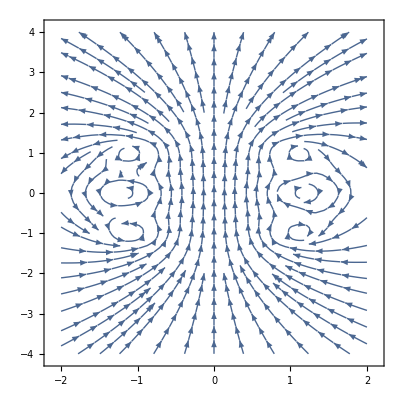

```mathematica
ListStreamPlot[data]
```